```mathematica
(*(*Uncomment to generate student list*)
Export["studentList.m",Table["Student "<>ToString[i],{i,1,30}]]*)

(*variables to change*)
students=Get[ToString[NotebookDirectory[]]<>"studentList.m"];
groupSize=6;
className="PHYS371";

(*variables calculated from inputs*)
numberofStudents=Length[students];
numberofGroups=Floor[numberofStudents/groupSize];
leftover=Mod[numberofStudents,groupSize];

(*check if groups are equally split*)
Echo["Are groups equally split? --> "<>ToString[leftover==0]];
groups=Table["Group "<>ToString[i],{i,1,numberofGroups}];
```

Are groups equally split? --> False

```mathematica
(*randomly assign groups*)
```

```mathematica
assignedGroups=Module[{remainingList=students,randomAssignment={},selectedStudent,selectCount},
(*iterate through number of groups*)
For[groupNumber=1,groupNumber≤numberofGroups,groupNumber++,
(*iterate through number of students, selecting random students for group assignment while adjusting the remainingList to select from*)
selectCount=0;
For[remainingStudents=numberofStudents-(groupNumber-1)*groupSize,remainingStudents>0,remainingStudents--,
selectedStudent=remainingList[[RandomInteger[{1,remainingStudents}]]];
selectCount++;
AppendTo[randomAssignment,groups[[groupNumber]]->selectedStudent
];
(*remove selectedStudent from remainingList*)
remainingList=DeleteCases[remainingList,selectedStudent];
(*terminate this loop to start a new group if we've hit the group threshhold*)
If[selectCount==groupSize,Break[]]
]
];
(*distribute any leftovers by iterating over groups starting at group 1, and adding one extra student*)
If[leftover≠0,
For[groupNumber=1,groupNumber≤leftover,groupNumber++,
selectedStudent=remainingList[[RandomInteger[{1,leftover}]]];
AppendTo[randomAssignment,groups[[groupNumber]]->selectedStudent];
remainingList=DeleteCases[remainingList,selectedStudent];
]
];
randomAssignment];
(*Check Number of Students selected matches size of class*)
Echo["Is everyone accounted for? --> "<>ToString[Length[assignedGroups]==numberofStudents]];
```

Part::partw: Part 3 of {Student 3} does not exist.

Is everyone accounted for? --> True

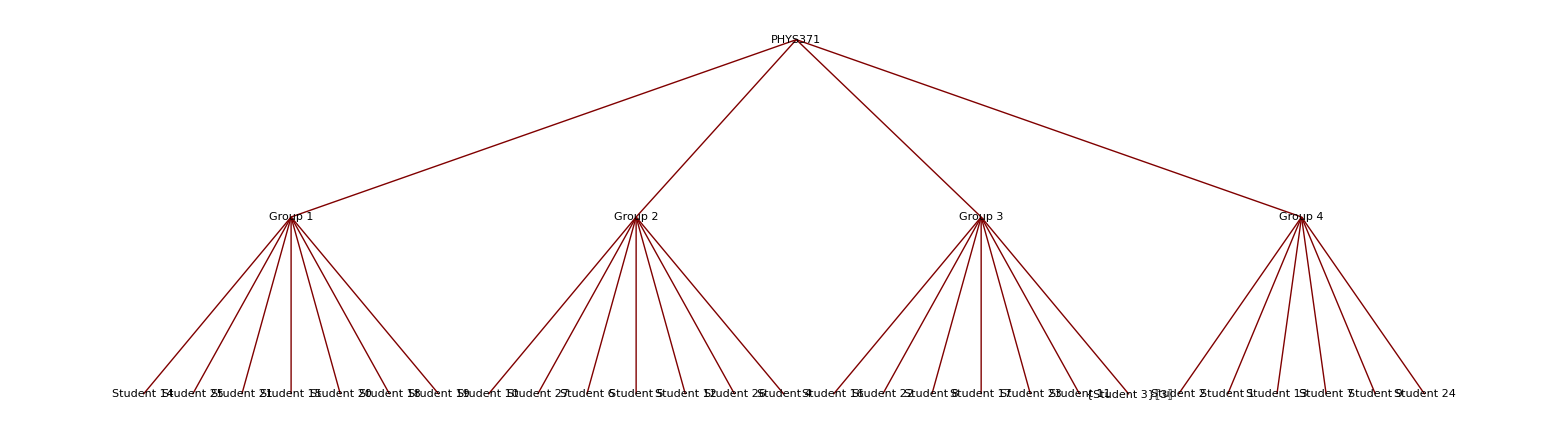

```mathematica
(*Plot Groupings*)
TreePlot[
Join[
Table[className->groups[[i]],{i,1,numberofGroups}],
assignedGroups
],
VertexLabeling->True]
```